## INITIALIZATION

```mathematica
dec8pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 8 2016\\**.tif"];
dec8files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 8 2016\\**.tif"];
```

```mathematica
dec9pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 9 2016\\**.tif"];
dec9files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 9 2016\\**.tif"];
```

```mathematica
dec10pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 10 2016\\**\\**\\**.tif"];
dec10files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 10 2016\\**\\**\\**.tif"];
```

```mathematica
dec12pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 12 2016\\**\\**\\**.tif"];
dec12files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 12 2016\\**\\**\\**.tif"];
```

```mathematica
dec13pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 13 2016\\**\\**\\**.tif"];
dec13files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 13 2016\\**\\**\\**.tif"];
```

```mathematica
dec14pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\**\\**\\**.tif"];
dec14files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\**\\**\\**.tif"];
```

```mathematica
GGroupDec14=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\Girls Group\\**\\**.tif"];
GGroupDec14files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\Girls Group\\**\\**.tif"];
GGroupDec14adj=ImageAdjust/@GGroupDec14[[All,1]];
```

```mathematica
allpics=Flatten[Join[{If[Length[#]==2,#[[1]],#]&/@dec8pics,If[Length[#]==2,#[[1]],#]&/@dec9pics,If[Length[#]==2,#[[1]],#]&/@dec10pics,If[Length[#]==2,#[[1]],#]&/@dec12pics,If[Length[#]==2,#[[1]],#]&/@dec14pics}]];
```

```mathematica
allpicsadj=ImageAdjust/@allpics;
```

```mathematica
allfiles=Flatten[Join[{dec8files,dec9files,dec10files,dec12files,dec14files}]];
```

## Binarize by Mean, Median

```mathematica
Manipulate[img=allpics[[i]];ColorNegate@Binarize[img,Method->"Cluster"],{i,1,Length[allpicsadj],1}]
```

Part::partd: Part specification allpics⟦97⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦97⟧.

ColorNegate::imginv: Binarize[allpics⟦97⟧,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

Part::partd: Part specification allpics⟦97⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦97⟧.

ColorNegate::imginv: Binarize[allpics⟦97⟧,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

Part::partd: Part specification allpics⟦97⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦97⟧.

ColorNegate::imginv: Binarize[allpics⟦97⟧,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

Part::partd: Part specification allpics⟦97⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦97⟧.

ColorNegate::imginv: Binarize[allpics⟦97⟧,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

```mathematica
Manipulate[img=allpics[[i]];ColorNegate@Binarize[img,Method->"MinimumError"],{i,1,Length[allpicsadj],1}]
```

Part::partd: Part specification allpics⟦135⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦135⟧.

ColorNegate::imginv: Binarize[allpics⟦135⟧,Method→MinimumError] should be a valid image, a color directive, or a list of such objects.

Part::partd: Part specification allpics⟦135⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦135⟧.

ColorNegate::imginv: Binarize[allpics⟦135⟧,Method→MinimumError] should be a valid image, a color directive, or a list of such objects.

Part::partd: Part specification allpics⟦135⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦135⟧.

ColorNegate::imginv: Binarize[allpics⟦135⟧,Method→MinimumError] should be a valid image, a color directive, or a list of such objects.

Part::partd: Part specification allpics⟦135⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦135⟧.

ColorNegate::imginv: Binarize[allpics⟦135⟧,Method→MinimumError] should be a valid image, a color directive, or a list of such objects.

```mathematica
cellDensityNew[pic_]:=Module[{k,z},k=EdgeDetect[pic,Method->"ShenCastan"];
z=Flatten[ImageData[k]];
N[Count[z,0]/Length[z]]]
```

```mathematica
cells=SelectComponents[i=ColorNegate@Binarize[allpics[[103]],Method->"Cluster"],{"Area","Holes","Circularity"},50<#1<750&&#2>0||#2>1&&.1<#3<100&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[i,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

```mathematica
Manipulate[cells=SelectComponents[i=ColorNegate@Binarize[allpics[[j]],Method->"Cluster"],{"Area","Circularity"},20<#1<750&&.1<#2<100&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[i,Graphics[{Red,Thick,Circle@@#&/@circles}]],{j,1,Length@allpics,1}]
```

Part::partd: Part specification allpics⟦5⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦5⟧.

ColorNegate::imginv: Binarize[allpics⟦5⟧,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

SelectComponents::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of ColorNegate[Binarize[allpics⟦5⟧,Method→Cluster]].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[ColorNegate[Binarize[allpics⟦5⟧,Method→Cluster]],{Area,Circularity},20<#1<750&&0.1<#2<100&].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of {Area,Circularity}.

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of Circle[Area,Circularity].

General::stop: Further output of ComponentMeasurements::invarg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ColorNegate[Binarize[allpics⟦5⟧,Method→Cluster]],].

Part::partd: Part specification allpics⟦5⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦5⟧.

ColorNegate::imginv: Binarize[allpics⟦5⟧,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

SelectComponents::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of ColorNegate[Binarize[allpics⟦5⟧,Method→Cluster]].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[ColorNegate[Binarize[allpics⟦5⟧,Method→Cluster]],{Area,Circularity},20<#1<750&&0.1<#2<100&].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of {Area,Circularity}.

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of Circle[Area,Circularity].

General::stop: Further output of ComponentMeasurements::invarg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ColorNegate[Binarize[allpics⟦5⟧,Method→Cluster]],].

```mathematica
cells=SelectComponents[i=ColorNegate@Binarize[allpics[[119]],Method->"Cluster"],{"Area","Circularity"},20<#1<750&&.1<#2<100&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
boxes=ComponentMeasurements[cells,{"BoundingBox"}][[All,2]];
Show[i,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

```mathematica
{{boxes[[1,1,1,1]],boxes[[1,1,1,2]]},{boxes[[1,1,2,1]],boxes[[1,1,2,2]]}}
```

{{542.,584.},{560.,598.}}

```mathematica
{{boxes[[1,1,1,1]]-10,boxes[[1,1,1,2]]+500},{boxes[[1,1,2,1]]-500,boxes[[1,1,2,2]]+500}}
```

{{42.,1084.},{60.,1098.}}

```mathematica
ImageTrim[,%]
```

-Graphics-

# RandomForest this btch

```mathematica
deadcells=Flatten@Table[ImageTrim[allpics[[k]],{{boxes[[j,1,1,1]]-20,boxes[[j,1,1,2]]-20},{boxes[[j,1,2,1]]+20,boxes[[j,1,2,2]]+20}}],{k,{97,103,115,117,118,119,120}},{j,1,42}];
```

```mathematica
livecells=Flatten@Table[ImageTrim[allpics[[k]],{{boxes[[j,1,1,1]]-20,boxes[[j,1,1,2]]-20},{boxes[[j,1,2,1]]+20,boxes[[j,1,2,2]]+20}}],{k,{1,2,3,4,5}},{j,1,42}];
```

```mathematica
aSdeadcells=Table[deadcells[[i]]->"Dead",{i,1,Length@deadcells}];
```

```mathematica
aSlivecells=Table[livecells[[i]]->"Live",{i,1,Length@livecells}];
```

```mathematica
ransamp=RandomSample@Join[aSdeadcells,aSlivecells];trainSet=ransamp[[;;Floor@(.8*Length@ransamp)]];testSet=ransamp[[Ceiling@(.8*Length@ransamp);;]];
```

```mathematica
c=Classify[trainSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[c,testSet]
```

ClassifierMeasurementsObject[…]

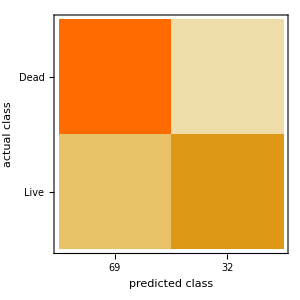

```mathematica
cm["ConfusionMatrixPlot"]
```

# CONVALUTIONAL NEURAL NET BBY

```mathematica
imgd=ImageDimensions/@deadcells;N/@{Mean[imgd[[All,1]]],Mean[imgd[[All,2]]]}
```

{50.1667,49.8095}

```mathematica
reSdeadcells=Flatten@Table[ImageResize[ImageTrim[allpics[[k]],{{boxes[[j,1,1,1]]-20,boxes[[j,1,1,2]]-20},{boxes[[j,1,2,1]]+20,boxes[[j,1,2,2]]+20}}],{50,50}],{k,{97,103,115,117,118,119,120}},{j,1,42}];
```

```mathematica
reSlivecells=Flatten@Table[ImageResize[ImageTrim[allpics[[k]],{{boxes[[j,1,1,1]]-20,boxes[[j,1,1,2]]-20},{boxes[[j,1,2,1]]+20,boxes[[j,1,2,2]]+20}}],{50,50}],{k,{1,2,3,4,5}},{j,1,42}];
```

```mathematica
aSrdeadcells=Table[reSdeadcells[[i]]->"Dead",{i,1,Length@deadcells}];
```

```mathematica
aSrlivecells=Table[reSlivecells[[i]]->"Live",{i,1,Length@livecells}];
```

```mathematica
ransampR=RandomSample@Join[aSrdeadcells,aSrlivecells];trainSet=ransampR[[;;Floor@(.8*Length@ransamp)]];testSet=ransampR[[Ceiling@(.8*Length@ransamp);;]];
```

## Encoders and Decoders

### Image encoder

```mathematica
enc=NetEncoder[{"Image",{50,50},ColorSpace->"Grayscale"}]
```

None

```mathematica
dec=NetDecoder[{"Class",{"Dead","Live"}}]
```

None

```mathematica
lenet=NetChain[
{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,100,Ramp,2,SoftmaxLayer[]},
"Output"->dec,"Input"->enc
]
```

Failure[…]

```mathematica
trainedNet=NetTrain[lenet,trainSet,MaxTrainingRounds->20]
```

Failure[…]

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\student\Documents\Cancer Bio Pics

```mathematica
Export["SIEMENSLiveDead.wlnet",trainedNet]
```

SIEMENSLiveDead.wlnet

```mathematica
trainedNet=Import["SIEMENSLiveDead.wlnet"]
```

NetChain[]

```mathematica
cmNet=ClassifierMeasurements[trainedNet,testSet]
```

ClassifierMeasurementsObject[…]

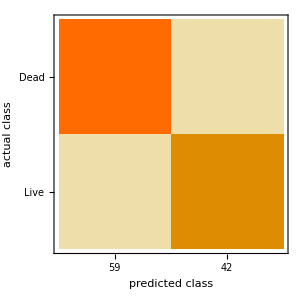

```mathematica
cmNet["ConfusionMatrixPlot"]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\student\Documents\Cancer Bio Pics

```mathematica
Export["confmatplot.png",-Graphics-]
```

confmatplot.png

```mathematica
cmNet["Precision"]
```

<|Dead→0.983051,Live→0.97619|>

```mathematica
trainedNet[ransampR[[2,1]]]
```

Dead

```mathematica
ransampR[[2,1]]
```

-Graphics-

```mathematica
reSlivecells[[4]]
```

-Graphics-

```mathematica
Tally[ImageDimensions/@allpics]
```

{{{800,600},165}}

```mathematica
Length@ransampR
```

504

## Run to calculate the CellDensity of each pic

```mathematica
AbsoluteTiming[cellDensities=Table[N@Total[(trainedNet/@Flatten@ImagePartition[allpics[[i]],{50,50}])/.{"Live"->1,"Dead"->0}]/192,{i,1,Length@allpics}];]
```

{250.776,Null}

```mathematica
cellDensities[[1;;10]]
```

{0.994792,0.989583,0.989583,1.,1.,0.994792,0.760417,0.984375,0.833333,0.776042}

```mathematica
Import["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 9 2016\\C1 A VC picture 1.tif"][[1]]
```

-Graphics-

```mathematica
tabs=Table[{cellDensities[[i]],allfiles[[i]]},{i,1,Length@allfiles}];
```

```mathematica
Length@allfiles
```

165

```mathematica
Length@cellDensities
```

165

```mathematica
Export["cellDensitiesList.xls",tabs]
```

cellDensitiesList.xls

```mathematica
Grid@tabs
```

0.994792 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\C1 1.tif
0.989583 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\C1 2.tif
0.989583 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\C2 1.tif
1. | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\C2 2.tif
1. | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\MLL-1 1.tif
0.994792 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\MLL-1 2.tif
0.760417 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\MLL-2 1.tif
0.984375 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\MLL-2 2.tif
0.833333 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\P1 1.tif
0.776042 | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\P2 1.tif
1. | C:\Users\student\Documents\Cancer Bio Pics\December 8 2016\P2 2.tif
0.239583 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 A Boys picture 1.tif
0.276042 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 A Boys picture 2.tif
0.375 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 A Girls picture 1.tif
0.447917 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 A Girls picture 2.tif
0.125 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 A VC picture 1.tif
0.135417 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 A VC picture 2.tif
0.677083 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 B Boys picture 1.tif
0.421875 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 B Boys picture 2.tif
0.505208 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 B Girls picture 1.tif
0.484375 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 B Girls picture 2.tif
0.328125 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 B VC picture 1.tif
0.34375 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C1 B VC picture 2.tif
0.427083 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C2 A Girls picture 1.tif
0.338542 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C2 A Girls picture 2.tif
0.380208 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C2 B Girls picture 1.tif
0.239583 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\C2 B Girls picture 2.tif
0.322917 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 1A Boys picture 1.tif
0.244792 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 1A Boys picture 2.tif
0.0989583 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 1B Boys picture 1.tif
0.0989583 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 1B Boys picture 2.tif
0.171875 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2A Boys picture 1.tif
0.0677083 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2A Boys picture 2.tif
0.125 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2A Girls picture 1.tif
0.166667 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2A Girls picture 2.tif
0.427083 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2A VC picture 1.tif
0.9375 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2A VC picture 2.tif
0.145833 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2B Boys picture 1.tif
0.166667 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2B Boys picture 2.tif
0.0885417 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2B Girls picture 1.tif
0.078125 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2B Girls picture 2.tif
0.213542 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2B VC picture 1.tif
0.369792 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\MLL 2B VC picture 2.tif
0.0885417 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 A Boys picture 1.tif
0.130208 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 A Boys picture 2.tif
0.244792 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 A Girls picture 1.tif
0.203125 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 A Girls picture 2.tif
0.166667 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 B Boys picture 1.tif
0.354167 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 B Boys picture 2.tif
0.171875 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 B Girls picture 1.tif
0.151042 | C:\Users\student\Documents\Cancer Bio Pics\December 9 2016\P1 B Girls picture 2.tif
0.776042 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\C cells\Boys C1 A Picture 1.tif
0.84375 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\C cells\Boys C1 A Picture 2.tif
0.776042 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\C cells\Boys C1 B picture1.tif
0.463542 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\C cells\Boys C1 B Picture 2.tif
0.151042 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL1 A Picture 1.tif
0.234375 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL1 A Picture 2.tif
0.0260417 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL1 B Picture 1.tif
0.0833333 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL1 B Picture 2.tif
0.0572917 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL2 A Picture 1.tif
0.078125 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL2 A Picture 2.tif
0.09375 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL2 B Picture 1.tif
0.104167 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\MLL cells\Boys MLL2 B Picture 2.tif
0.0885417 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\P cells\Boys P1 A Picture 1.tif
0.0989583 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\P cells\Boys P1 A Picture 2.tif
0.078125 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\P cells\Boys P1 B Picture 1.tif
0.0729167 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Boys group\P cells\Boys P1 B Picture 2.tif
0.416667 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\C cells\VC C1 A Picture 1.tif
0.354167 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\C cells\VC C1 A Picture 2.tif
0.0729167 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\C cells\VC C1 B Picture 1.tif
0.354167 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\C cells\VC C1 B Picture 2.tif
0.119792 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\MLL cells\VC MLL2 A Picture 1.tif
0.119792 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\MLL cells\VC MLL2 A Picture 2.tif
0.239583 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\MLL cells\VC MLL2 B Picture 1.tif
0.197917 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Dr. Chinwalla\MLL cells\VC MLL2 B Picture 2.tif
0.588542 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C1 A Picture 1.tif
0.65625 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C1 A Picture 2.tif
0.817708 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C1 B Picture 1.tif
0.838542 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C1 B Picture 2.tif
0.588542 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C2 A Picture 1.tif
0.53125 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C2 A Picture 2.tif
0.625 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C2 B Picture 1.tif
0.572917 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\C cells\Girls C2 B Picture 2.tif
0.161458 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\MLL cells\Girls MLL2 A Picture 1.tif
0.09375 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\MLL cells\Girls MLL2 A Picture 2.tif
0.119792 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\MLL cells\Girls MLL2 B Picture 1.tif
0.0833333 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\MLL cells\Girls MLL2 B Picture 2.tif
0.0677083 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\P cells\Girls P1 A Picture 1.tif
0.125 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\P cells\Girls P1 A Picture 2.tif
0.197917 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\P cells\Girls P1 B Picture 1.tif
0.182292 | C:\Users\student\Documents\Cancer Bio Pics\December 10 2016\Girls group\P cells\Girls P1 B Picture 2.tif
0.9375 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\C1 Cells\Boys C1 A 1.tif
0.963542 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\C1 Cells\Boys C1 A 2.tif
0.963542 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\C1 Cells\Boys C1 B 1.tif
0.90625 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\C1 Cells\Boys C1 B 2.tif
0.0364583 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL1 Cells\Boys MLL1 A 1.tif
0.0364583 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL1 Cells\Boys MLL1 A 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL1 Cells\Boys MLL1 B 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL1 Cells\Boys MLL1 B 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL2 Cells\Boys MLL2 A 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL2 Cells\Boys MLL2 A 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL2 Cells\Boys MLL2 B 1.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\MLL2 Cells\Boys MLL2 B 2.tif
0.0104167 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\P1 Cells\Boys P1 A 1.tif
0.0104167 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\P1 Cells\Boys P1 A 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\P1 Cells\Boys P1 B 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Boys\P1 Cells\Boys P1 B 2.tif
0.760417 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\C1 Cells\VC C1 A 1.tif
0.770833 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\C1 Cells\VC C1 A 2.tif
0.515625 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\C1 Cells\VC C1 B 1.tif
0.59375 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\C1 Cells\VC C1 B 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\MLL2 Cells\VC MLL2 A 1.tif
0.03125 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\MLL2 Cells\VC MLL2 A 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\MLL2 Cells\VC MLL2 B 1.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Dr Chinwalla\MLL2 Cells\VC MLL2 B 2.tif
0.208333 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\C cells\Girls C1 A pic.tif
0.015625 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\C cells\Girls C1 B pic.tif
0.0416667 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\C cells\Girls C2 A pic.tif
0.0364583 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\C cells\Girls C2 B pic.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\MLL2\Girls MLL2 A pic.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\MLL2\Girls MLL2 B pic.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\P1\Girls P1 A pic.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 12 2016\Girls\P1\Girls P1 B pic.tif
0.932292 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\C group\Boys C1 A Picture 1.tif
0.895833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\C group\Boys C1 A Picture 2.tif
1. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\C group\Boys C1 B Picture 1.tif
0.984375 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\C group\Boys C1 B Picture 2.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL1 A Picture 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL1 A Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL1 B Picture 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL1 B Picture 2.tif
0.0208333 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL1 B Picture 3.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL2 A Picture 1.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL2 A Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL2 B Picture 1.tif
0.015625 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\MLL Group\Boys MLL2 B Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\P group\Boys P1 A Picture 1.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\P group\Boys P1 A Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\P group\Boys P1 B Picture 1.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Boys Group\P group\Boys P1 B Picture 2.tif
0.875 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\C group\VC C1 A Picture 1.tif
0.458333 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\C group\VC C1 A Picture 2.tif
0.973958 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\C group\VC C1 B Picture 1.tif
0.697917 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\C group\VC C1 B Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\MLL Group\VC MLL2 A Picture 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\MLL Group\VC MLL2 A Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\MLL Group\VC MLL2 B Picture 1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Dr. Chinwalla\MLL Group\VC MLL2 B Picture 2.tif
0.0416667 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 A Picture 1 Anomaly.tif
0.0364583 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 A Picture 2.tif
0.0572917 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 A Picture 3.tif
0.015625 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 B Picture 1.tif
0.0572917 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 B Picture 2.tif
0.0208333 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 A Picture 1.tif
0.0104167 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 A Picture 2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 B Picture 1.tif
0.015625 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 B Picture 2.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 A Picture 1.tif
0.0104167 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 A Picture 2.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 B Picture1.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 B Picture2.tif
0. | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 A Picture 1.tif
0.0104167 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 A Picture 2.tif
0.0104167 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 B Picture 1.tif
0.00520833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 B Picture 2.tif

### Saved CNN

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\student\Documents\Cancer Bio Pics

```mathematica
Export["LiveDeadCell.wlnet",trainedNet]
```

LiveDeadCell.wlnet